## Ряды Лорана

Для того чтобы заставить Mathematica раскладывать функции в ряд Лорана применим следующее свойство:

##### Связь между рядом Лорана и рядом Фурье:

Пусть функция f(z) регулярна в кольце r_1< |z|<1+r_2 (0≤ r_1<1, r_2>0) содержащем единичную окружность |z|=1. Тогда она представляется в этом кольце рядом лорана:

f(z)=∑_(n=-∞)^∞ c_n z^n

Откуда, полагая f(z)=ⅇ^iϕ, получаем разложения в ряд Фурье функции:

F(ϕ)=f(ⅇ^iϕ)=∑_(n=-∞)^∞ c_n ⅇ^(ⅈ ϕ n)

Отсюда следует обратное: если функция F(ϕ) представляется в виде: F(ϕ)=f(ⅇ^(ⅈ ϕ)) , где функция f(z) регулярна в кольце, то ряд (2) является рядом Фурье для F(ϕ).

##### Рассмотрим пример 12.352

Найти все разложенияуказанных функций в ряды Лорана по степеням z-z_0.

f(z)=1/(z(z-1)),z_0=1

Зададим функцию

```mathematica
f[z_]:=1/(z(z-1))
```

Из “стандартного” набора функций имеет функцию Series[ f[z], {z , z_0, n} ] которая раскладывает функцию в ряд Тейлора\Лорана по степеням z-z_0 до n-ого члена.

Проблема в том, что с помощью этой функции можно получить лишь одно разложение вблизи точки z_0:

```mathematica
Series[1/(z(z-1)),{z,1,4}]
```

1/(z-1)-1+(z-1)-(z-1)^2+(z-1)^3-(z-1)^4+O[z-1]^5

Для того чтобы получить разложение в ряд Лорана в разных кольцах, воспользуемся утверждением, описанным выше.

Mathematica может раскладывать функции в ряд Фурье. Изобразим особые точки функции f(z),выберем контур С, составим множество коэффициентов ряда Фурье для этого контура, и затем сформируем из них ряд Лорана.

```mathematica
Graphics[{Circle[{1,0},1/2],Circle[{1,0},3/2],Text["r1",{1/2,1/2}],Text["r2",{3/2,3/2}],PointSize[Large],Red,Point[ReIm[z/.Solve[f[z]^-1==0,z]]]},PlotRange->{{-3,3},{-3,3}},Frame->False,Axes->True,AxesLabel->{Re,Im}]
```

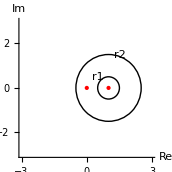

Найдем коэффициенты ряда Лорана (Фурье) при 0< |z-1|<1 . Для этого выберем контур r1 и воспользуемся функцией FourierCoefficient.

```mathematica
With[{r=1/2,n=8,z0=1},Table[{k,FourierCoefficient[With[{z=z0+r Exp[I t]},f[z]],t,k]/r^k  },{k,-n,n}]]
```

{{-8,0},{-7,0},{-6,0},{-5,0},{-4,0},{-3,0},{-2,0},{-1,1},{0,-1},{1,1},{2,-1},{3,1},{4,-1},{5,1},{6,-1},{7,1},{8,-1}}

Это множество имеент вид: {k,c_k}

Составим ряд Лорана вида:

f(z)=∑_(n=-N)^N (c_n(z-z_0))^n

```mathematica
lor[z_,n1_,r1_,z01_]:=Total@With[{r=r1,n=n1,z0=z01},Table[(z-z0)^k FourierCoefficient[With[{z1=z0+r Exp[I t]},f[z1]],t,k]/r^k  ,{k,-n,n}]]
```

```mathematica
lor[z,8,1/2,1]
```

-2+1/(-1+z)-(-1+z)^2+(-1+z)^3-(-1+z)^4+(-1+z)^5-(-1+z)^6+(-1+z)^7-(-1+z)^8+z

Теперь можно найти разложение функции при |z-1| >1:

```mathematica
lor[z,8,3/2,1]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Расширим функцию, добавив функцию f[z] как аргумент:

```mathematica
loran[z_,expr_,z01_,r1_,n1_]:=Total@With[{r=r1,n=n1,z0=z01},Table[(z-z0)^k FourierCoefficient[With[{z1=z0+r Exp[I t]},expr/.z->z1],t,k]/r^k  ,{k,-n,n}]]
```

Воспользуемся этим методом для функции:

Видно что в увеличением степени разложения (до 15) ряд в точке 15 стремится к значению функции в данной точке.

```mathematica
loran[z,1/(z (z-1)),8,2,0]
```

1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2